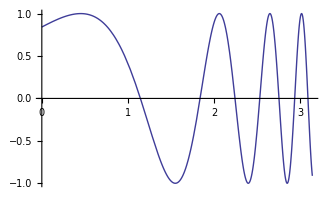

```mathematica
Plot[Sin[Exp[x]],{x,0,Pi}]
```

```mathematica
Solve[{a x + b y == 1, x + y ==2},{x,y}]
```

{{x→-(-1+2 b)/(a-b),y→2-1/(a-b)+(2 b)/(a-b)}}

```mathematica
Solve[{E == p + 1/2 rho u^2, t = 4 E / rho u^2, r = rho/Sqrt[Pi t]},{p,rho,u}]
```

Solve::naqs: ⅇ == p + rho\ u^2/2 && 4\ ⅇ\ u^2/rho && rho/2\ √ⅇ\ π\ √u^2/rho is not a quantified system of equations and inequalities.

Solve[{ⅇ==p+(rho u^2)/2,(4 ⅇ u^2)/rho,rho/(2 √(ⅇ π) √(u^2/rho))},{p,rho,u}]

```mathematica
Solve[{E == p + 1/2 rho u^2, t == 4 E / rho u^2, r == rho/Sqrt[Pi t]},{p,rho,u}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p→1/2 (2 ⅇ-rho u^2)}}

```mathematica
Solve[{E == p + 1/2 rho u^2, t = 4 E / rho u^2-2 u^2, r = rho/Sqrt[Pi t]},{p,rho,u}]
```

Solve::naqs: ⅇ == p + rho\ u^2/2 && -2\ u^2 + 4\ ⅇ\ u^2/rho && rho/√π\ √-2\ u^2 + 4\ ⅇ\ u^2/rho is not a quantified system of equations and inequalities.

Solve[{ⅇ==p+(rho u^2)/2,-2 u^2+(4 ⅇ u^2)/rho,rho/(√π √(-2 u^2+(4 ⅇ u^2)/rho))},{p,rho,u}]

```mathematica
Solve[{E == p + 1/2 rho u^2, t == 4 E / rho u^2 -2u^2, r == rho/Sqrt[Pi t]},{p,rho,u}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p→1/2 (2 ⅇ-rho u^2)}}

```mathematica
Solve[{E == p + 1/2 rho u^2, t == 4 E / rho u^2 -2u^2, r == rho/Sqrt[Pi t]},{p,rho}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{rho→(2 ⅇ)/u^2-(2 p)/u^2}}

```mathematica
Solve[{E == p + 1/2 rho u^2, t == 4 E / rho  -2u^2, r == rho/Sqrt[Pi t]},{p,rho,u}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p→1/2 (2 ⅇ-rho),u→-1},{p→1/2 (2 ⅇ-rho),u→1}}